0.443333

-0.539029

0.134757

0.

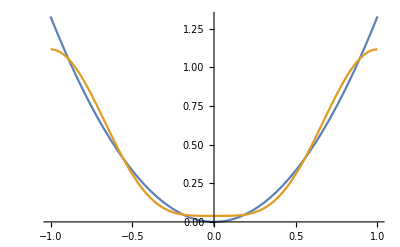

```mathematica
f[t_] :=p*t^2;
p=1.330;
T=2;
ω0=2π/T;
a0=1/T  Integrate[f[t],{t,-1,1}]
a1=2/T  Integrate[f[t]Cos[ω0 t],{t,-1,1}]
a2=2/T  Integrate[f[t]Cos[2ω0 t],{t,-1,1}]
b1=2/T  Integrate[f[t]Sin[2ω0 t],{t,-1,1}]
F[t_]:=a0+a1 Cos[ω0 t]+a2 Cos[2ω0 t];
Plot[{f[t], F[t]}, {t,-1,1}]
```

```mathematica
w[t_]:=a t^2 +b t+c
Integrate[(F[t]-w[t])t^2, {t,-1,1}]
Integrate[(F[t]-w[t])t, {t,-1,1}]
Integrate[(F[t]-w[t]), {t,-1,1}]
```

0.527669-0.4 a-0.666667 c

0.-0.666667 b

-0.666667 (-1.33+a+3. c)

```mathematica
eq1=0.5276694143339684-0.4 a-0.6666666666666666 c==0;
eq2=0.-0.6666666666666666 b==0;
eq3=-0.6666666666666666 (-1.33+a+3. c)==0;
Solve[{eq1,eq2,eq3},{a,b,c}]
```

{{a→1.30564,b→0.,c→0.00811985}}